# Mathematica

It is the name of the software.
It works like Excel when we’re going to use a formulae, we have to be careful with what we use, the name, the list of parameters, etc.
There is a programming language involved, its name is Wolfram Language.
Mathematica offers plenty of tools, the most of them (we, here, now, are not interested in).
This presentation intention is to go as directly as possible to model and simulate

## Notebook

Or the way we must use in order to communicate with the kernel (of Wolfram).
We can create a document like this one.
We can interact with the kernel using Wolfram Language.
What we insert:

Title

Subtitle

Chapter

Section

Subsection

Subsubsection

Text

Code

Input

## Math operations

```mathematica
13+2
```

```mathematica
13-2
```

```mathematica
13*2
```

```mathematica
13/2
```

Numerical Value

```mathematica
N[23/3]
```

Square Brackets

```mathematica
N[23/3,2]
```

```mathematica
N[23/3,3]
```

```mathematica
N[23/3,4]
```

Free-Form input

23/3

```mathematica
Mod[23,2]
```

```mathematica
Quotient[23,2]
```

```mathematica
Round[23/3]
```

```mathematica
Round[23/3,2]
```

```mathematica
Round[23/3,3]
```

```mathematica
Round[23/3,4]
```

```mathematica
Round[23/3,5]
```

```mathematica
13/3
```

13/3

```mathematica
N[13/3]
```

4.33333

## Functions

```mathematica
Plus[2,3]
```

5

```mathematica
Subtract[5,2]
```

3

```mathematica
Times[2,3]
```

6

```mathematica
Times[2,Plus[3,4]]
```

14

```mathematica
Divide[7,2]
```

7/2

```mathematica
Power[3,2]
```

9

```mathematica
Max[2,7,3]
```

7

```mathematica
Max[{2,7,3}]
```

7

```mathematica
Min[2,7,3]
```

2

```mathematica
RandomInteger[10]
```

3

## Variables

```mathematica
rate = .18
```

```mathematica
3000 *rate
```

Case sensitive

```mathematica
Pi*14^2
```

```mathematica
pi*14^2
```

## Lists

alist = {2,3,4,5,19}

Curly Braces

```mathematica
Length[alist]
```

```mathematica
Count[alist]
```

```mathematica
Min[alist]
```

```mathematica
Max[alist]
```

```mathematica
Total[alist]
```

```mathematica
Mean[alist]
```

```mathematica
Range[7]
```

```mathematica
Range[2,11]
```

```mathematica
Range[3,12,.5]
```

```mathematica
Goes to operator
```

## More Lists

```mathematica
blist = {2, 7, 8, 3, 11, 4, 5, 19}
```

{2,7,8,3,11,4,5,19}

```mathematica
Sort[blist, Greater]
```

{19,11,8,7,5,4,3,2}

```mathematica
blist
```

{2,7,8,3,11,4,5,19}

```mathematica
Sort[blist,Less]
```

{2,3,4,5,7,8,11,19}

```mathematica
Reverse[blist]
```

{19,5,4,11,3,8,7,2}

## Symbolic expressions

```mathematica
Solve[a x^2+b x+c==0, x]/.{a->1,b->1,c->-5}
```

{{x→1/2 (-1-√21)},{x→1/2 (-1+√21)}}

```mathematica
{a->1,b->1,c->1}
```

{a→1,b→1,c→1}

```mathematica
GatherBy[{a->1,b->1,c->1},Last]
```

{{a→1,b→1,c→1}}

WolframAlphaQueryParseResults

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

WolframAlphaQueryParseResults

{1,4,9,16,25}

```mathematica
CountryData["Peru","LifeExpectancy"]
```

74.96 yr

WolframAlphaQueryResults

```mathematica
caffeine  molecule
```

Molecule[…]

toast + orange juice

WolframAlphaQueryResults

-Graphics-

## Last output cell

```mathematica
Table[i^2,{i,1,15}]
```

```mathematica
Total[%]
```

```mathematica
=Visualize the table of values for i^2, where i goes from 1 to 15.
```

## Create a function

```mathematica
doubleIt[x_]:=x*2
```

```mathematica
doubleIt[8]
```

```mathematica
powerOf[x_,exp_]:=x^exp
```

```mathematica
powerOf[3,2]
```

## Matrices

```mathematica
amat={{1,2,3,4},{2,-1,5,-2}}
```

```mathematica
Dimensions[amat]
```

```mathematica
bmat={{3,-1},{-2,3},{1,-2},{-1,3}}
```

```mathematica
Dimensions[bmat]
```

```mathematica
cmat=amat.bmat
```

{{-2,11},{15,-21}}

```mathematica
Dimensions[cmat]
```

{2,2}

```mathematica
Det[cmat]
```

-123

```mathematica
cmati=Inverse[cmat]
```

{{7/41,11/123},{5/41,2/123}}

```mathematica
cmati //N//MatrixForm
```

(0.170732 | 0.0894309
0.121951 | 0.0162602)

```mathematica
MatrixForm[cmat.cmati]
```

(1 | 0
0 | 1)

```mathematica
cmat+cmati //N // MatrixForm
```

(-1.82927 | 11.0894
15.122 | -20.9837)

```mathematica
cmat-cmati //N // MatrixForm
```

(-2.17073 | 10.9106
14.878 | -21.0163)

```mathematica
MatrixForm[amat]
```

(1 | 2 | 3 | 4
2 | -1 | 5 | -2)

```mathematica
MatrixForm[Transpose[amat]]
```

(1 | 2
2 | -1
3 | 5
4 | -2)

## Referring to matrix rows and columns

```mathematica
mat1={{3,4,5,8},{-1,-3,-2,6},{9,-2,1,3}}
```

{{3,4,5,8},{-1,-3,-2,6},{9,-2,1,3}}

```mathematica
MatrixForm[mat1]
```

(3 | 4 | 5 | 8
-1 | -3 | -2 | 6
9 | -2 | 1 | 3)

```mathematica
mat1[[2]] (*row*)
```

{-1,-99,-2,6}

```mathematica
mat1[[All,2]]  (*Column*)
```

{4,-99,-2}

```mathematica
mat1[[2,2]]
```

-3

```mathematica
mat1[[2,2]]=-99
```

-99

```mathematica
MatrixForm[mat1]
```

(3 | 4 | 5 | 8
-1 | -99 | -2 | 6
9 | -2 | 1 | 3)

## Plot a function

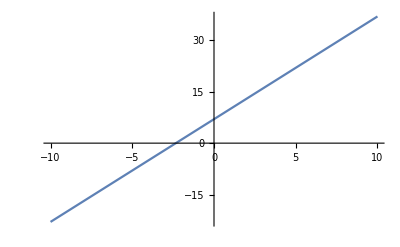

```mathematica
Plot[3x+7,{x,-10,10}]
```

WolframAlphaQueryParseResults

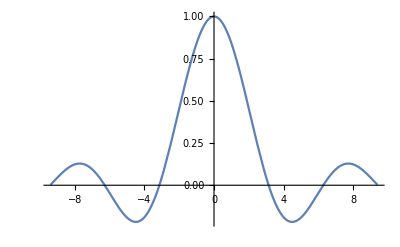

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
Manipulate[
Plot[m*x+b,{x,-10,10}, PlotRange->{-10,10}], 
{m, -9,9}, {b,-8.9,8.9}]
```

```mathematica
Manipulate[Plot[amp*Sin[freq*x],{x,0,2π}, PlotRange->{-6,6}],{freq,1,5}, {amp,1,7}]
```

```mathematica
(sin(x))/xx0
```

1

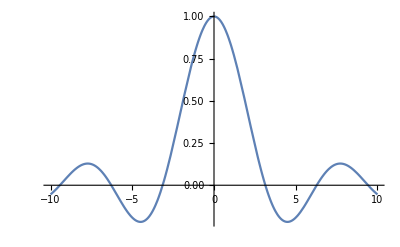

```mathematica
Plot[Sin[x]/x,{x,-10,10}]
```

```mathematica
Integrate[x^3*Sin[x], {x, 0, 2*Pi}]
```

```mathematica
A^2 // TraditionalForm
```

A^2

```mathematica
D[5 x^3-2 x^2+1,x]
```

-4 x+15 x^2

```mathematica
D[5 x^3-2 x^2+1,{x,2}]
```

-4+30 x

```mathematica
D[Cos[x],{x,n}]
```

Cos[(n π)/2+x]